## xAct

```mathematica
<<xAct`xCoba`;
<<xAct`xPert`;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
DefManifold[M,4,IndexRange[b,l]];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefChart[kerr,M,{0,1,2,3},{t[],r[],θ[],ϕ[]}];
```

** DefChart: Defining chart kerr.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping kerr.

** DefMapping: Defining inverse mapping ikerr.

** DefTensor: Defining mapping differential tensor dikerr[-a,ikerrb].

** DefTensor: Defining mapping differential tensor dkerr[-b,kerra].

** DefBasis: Defining basis kerr. Coordinated basis.

** DefCovD: Defining parallel derivative PDkerr[-b].

** DefTensor: Defining vanishing torsion tensor TorsionPDkerr[b,-c,-d].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDkerr[b,-c,-d].

** DefTensor: Defining vanishing Riemann tensor RiemannPDkerr[-b,-c,-d,e].

** DefTensor: Defining vanishing Ricci tensor RicciPDkerr[-b,-c].

** DefTensor: Defining antisymmetric +1 density etaUpkerr[b,c,d,e].

** DefTensor: Defining antisymmetric -1 density etaDownkerr[-b,-c,-d,-e].

```mathematica
DefScalarFunction/@{f1,w1,l1,m1};
```

** DefScalarFunction: Defining scalar function f1.

** DefScalarFunction: Defining scalar function w1.

** DefScalarFunction: Defining scalar function l1.

** DefScalarFunction: Defining scalar function m1.

```mathematica
metricS=CTensor[{{-f1[r[]],0,0,0},{0,m1[r[]],0,0},{0,0,m1[r[]] r[]^2,0},{0,0,0,m1[r[]] r[]^2 Sin[θ[]]^2}},{-kerr,-kerr}];
```

```mathematica
SetCMetric[metricS,kerr,SignatureOfMetric->{3,1,0}];
```

```mathematica
MetricCompute[metricS,kerr,All];
```

```mathematica
cd=CovDOfMetric[metricS];
```

```mathematica
rule1={r[]->r,θ[]->θ};
```

```mathematica
Gmuupnulower=(Table[Einstein[cd][{i,kerr},{j,-kerr}],{i,0,3},{j,0,3}])//.rule1
```

{{(8 m1[r] m1'[r]-3 r m1'[r]^2+4 r m1[r] m1''[r])/(4 r m1[r]^3),0,0,0},{0,(4 m1[r]^2 f1'[r]+2 m1[r] (2 f1[r]+r f1'[r]) m1'[r]+r f1[r] m1'[r]^2)/(4 r f1[r] m1[r]^3),0,0},{0,0,(-(r f1'[r]^2)/f1[r]^2+(2 (f1'[r]+r f1''[r]))/f1[r]+(-2 r m1'[r]^2+2 m1[r] (m1'[r]+r m1''[r]))/m1[r]^2)/(4 r m1[r]),0},{0,0,0,(-r m1[r]^2 f1'[r]^2+2 f1[r] m1[r]^2 (f1'[r]+r f1''[r])+2 f1[r]^2 (-r m1'[r]^2+m1[r] (m1'[r]+r m1''[r])))/(4 r f1[r]^2 m1[r]^3)}}

```mathematica
Gmuupnulower[[3,3]]-Gmuupnulower[[4,4]]//Expand//FullSimplify
```

```mathematica
Gmuupnulower[[1,1]]
```

(8 m1[r] m1'[r]-3 r m1'[r]^2+4 r m1[r] m1''[r])/(4 r m1[r]^3)

```mathematica
Gmuupnulower[[2,2]]
```

(4 m1[r]^2 f1'[r]+2 m1[r] (2 f1[r]+r f1'[r]) m1'[r]+r f1[r] m1'[r]^2)/(4 r f1[r] m1[r]^3)

```mathematica
Quit[]
```

```mathematica
rule1={r->rH/(1-x)};
rule2={f1'[r ]->f1'[x ]/(rH/(1-x))(1-x),m1'[r ]->m1'[x ]/(rH/(1-x))(1-x)};
rule4={f1''[r ]->1/(rH/(1-x))^2((1-x)^2 f1''[x ]-2(1-x)f1'[x ]),m1''[r ]->1/(rH/(1-x))^2((1-x)^2 m1''[x ]-2(1-x)m1'[x ])};
rule7={f1[r ]->f1[x ],m1[r ]->m1[x ],rho[r]->rho[x]};
```

```mathematica
eq1=(8 m1[r] m1'[r]-3 r m1'[r]^2+4 r m1[r] m1''[r])/(4 r m1[r]^3)+rho[x]//.rule7//.rule4//.rule2//.rule1//Simplify
```

(4 rH^2 m1[x]^3 rho[x]-3 (-1+x)^4 m1'[x]^2+4 (-1+x)^4 m1[x] m1''[x])/(4 rH^2 m1[x]^3)

```mathematica
eq2=(4 m1[r]^2 f1'[r]+2 m1[r] (2 f1[r]+r f1'[r]) m1'[r]+r f1[r] m1'[r]^2)/(4 r f1[r] m1[r]^3)//.rule7//.rule4//.rule2//.rule1//Simplify
```

((-1+x)^3 (-4 m1[x]^2 f1'[x]-2 m1[x] (2 f1[x]-(-1+x) f1'[x]) m1'[x]+(-1+x) f1[x] m1'[x]^2))/(4 rH^2 f1[x] m1[x]^3)

```mathematica
rho[x_]:=-(alpha (beta+2 M) rH (-1+x)^4 x^2)/(2 π (M (-1+x)-rH (2-2 x+x^2))^2 (beta (-1+x)+M (-1+x)-rH (2-2 x+x^2))^3);
```

```mathematica
eq1=eq1/.{alpha->10,beta->10,rH->1,M->2}//Expand//Simplify
```

((-1+x)^4 (280 x^2 m1[x]^3-3 π (-2+x)^4 (14-14 x+x^2)^3 m1'[x]^2+4 π (-2+x)^4 (14-14 x+x^2)^3 m1[x] m1''[x]))/(4 π (-2+x)^4 (14-14 x+x^2)^3 m1[x]^3)

```mathematica
eq2=eq2/.{alpha->10,beta->10,rH->1,M->2}//Expand//Simplify
```

((-1+x)^3 (-4 m1[x]^2 f1'[x]-2 m1[x] (2 f1[x]-(-1+x) f1'[x]) m1'[x]+(-1+x) f1[x] m1'[x]^2))/(4 f1[x] m1[x]^3)

```mathematica
Solve[eq1==0,m1''[x]]//FullSimplify
```

{{m1''[x]→-(70 x^2 m1[x]^2)/(π (-2+x)^4 (14+(-14+x) x)^3)+(3 m1'[x]^2)/(4 m1[x])}}

```mathematica
Solve[eq2==0,f1'[x]]//FullSimplify
```

{{f1'[x]→(f1[x] m1'[x] (-4 m1[x]+(-1+x) m1'[x]))/(4 m1[x]^2-2 (-1+x) m1[x] m1'[x])}}

```mathematica
sol2=NDSolve[{m1''[x]==-(70 x^2 m1[x]^2)/(π (-2+x)^4 (14+(-14+x) x)^3)+(3 m1'[x]^2)/(4 m1[x]),f1'[x]==(f1[x] m1'[x] (-4 m1[x]+(-1+x) m1'[x]))/(4 m1[x]^2-2 (-1+x) m1[x] m1'[x]),f1[1]==1,m1[1]==1,f1[0]==0},{f1,m1},{x,0,1},AccuracyGoal->18,MaxSteps->10^6,WorkingPrecision->32]
```

{{f1→InterpolatingFunction[…],m1→InterpolatingFunction[…]}}

```mathematica
f1[x]/x^2/.sol2[[1]]/.x->0.5
```

0.419447

## Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["sol_alpha100000_beta100000_tol006_it-3_rH100_chi000_n061_m31.dat","Table"];
```

```mathematica
xlist=data[[2;;61,1]];
```

```mathematica
fbarlist=Table[f1[x]/x^2/.sol2[[1]],{x,xlist}];
```

```mathematica
mbarlist=Table[(f1[x]m1[x])/x^2/.sol2[[1]],{x,xlist}];
```

```mathematica
Export["SchDMprove.dat",Transpose[{xlist,fbarlist,mbarlist}]];
```

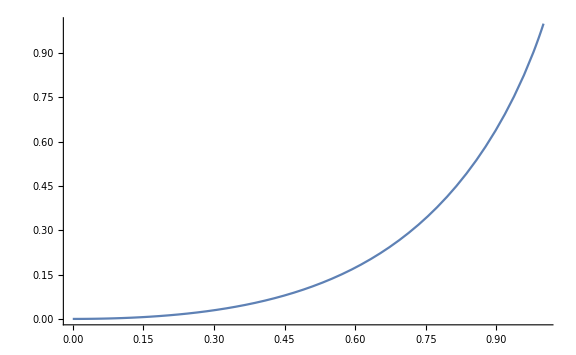

```mathematica
Plot[f1[x]/.sol2[[1]],{x,0,1},PlotRange->All]
```